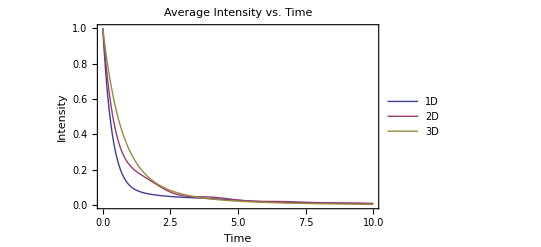

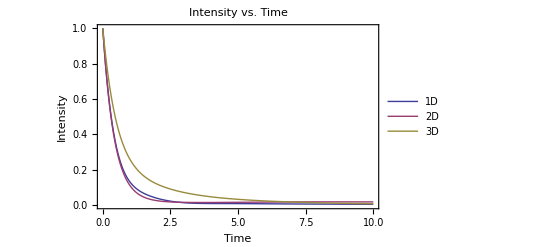
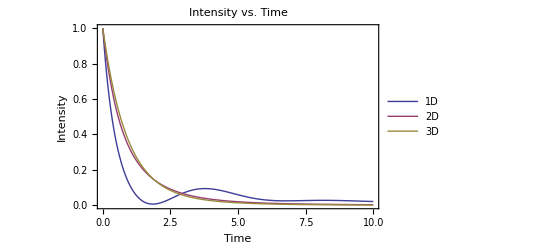
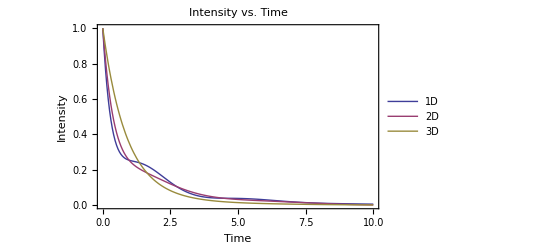
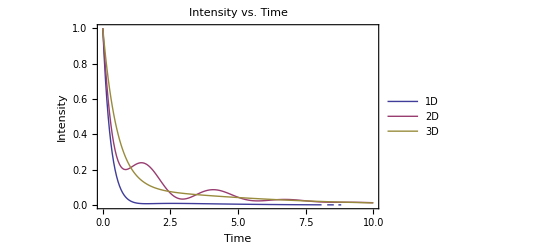
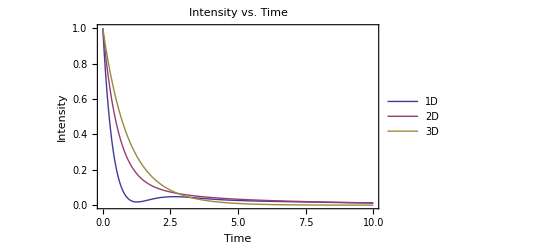

4 Particles

randomPlacement is True
randomOrientation is False
equalEnergies is False

Positions:
{x, y, z}
0.719834   0.940961   0.135029

0.134665   0.757421   0.970743

0.934967   0.706513   0.386725

0.718246   0.319058   0.302794

 Orientations:
{ρ, θ, ϕ}
     Pi   Pi
     --   --
1    2    2

     Pi   Pi
     --   --
1    2    2

     Pi   Pi
     --   --
1    2    2

     Pi   Pi
     --   --
1    2    2

```mathematica
(*The ultimate goal of this program is to graph the intensity of light coming from a set of interacting particles over time using the equation I=∑Subscript[γ, αβ] Subscript[x, αβ], where Subscript[x, αβ] is the solution to the differential equation Subscript[ẋ, αβ]=ⅈ(Subscript[ϵ, α]-Subscript[ϵ, β])Subscript[x, αβ]-ⅈ∑_γ (Subscript[Ω, γα] Subscript[x, γβ]-Subscript[Ω, βγ] Subscript[x, αγ])+1/2∑_γ (Subscript[Γ, γα] Subscript[x, γβ]+Subscript[Γ, βγ] Subscript[x, αγ]). The positions of particles can be randomized or chosen, their orientations can all go in a specific direction or point in different directions, and their energies can be the same or slightly different. Commands to change these options are listed and explained below*)

SetDirectory[NotebookDirectory[]]; 
Off[Power::infy]
Off[Infinity::indet]
Off[Part::pspec]
Off[Part::span]
Off[NSum::nslim]
Off[Set::partd]
Off[Set::partw]

(*Used to choose certain conditions under which the code runs. runCount is how many times it goes through the program. fileTitle is the name under which each plot will be saved. The multipleRun and averagePlot tables represent all of the final graphs and the average in each dimension*)
fileTitle=testTitle; (*The name the files will be saved under once the program runs*)
runCount=5; (*How many times the program runs*)
multipleRun=Table[i,{i,1,runCount}];
averagePlotX1=Table[i,{i,1,runCount}];
averagePlotY1=Table[i,{i,1,runCount}];
averagePlotZ1=Table[i,{i,1,runCount}];

(*The calculation itself. The variable the "Do" command uses is "o," so you can change conditions between each individual run by making other variables a function of "o"*)
Do[
(*numParticles is the number of particles and vectorValues represents their positions. particlePositions allows you to choose specific locations for the particles. Turn randomPlacement to "True" or "False" depending on whether you want a set of randomly distributed particles or particles at the locations determined in particlePositions. randomOrientation decides whether or not the orientation of each particle's dipole is randomized or in a set direction, and sameOrientation decides whether they all point in the same direction or the directions denoted by particleOrientations. randomOrientation overrides samOrientation, so even if sameOrientation is "True," randomOrientation will have to be set to "False" for the program to acknowledge that. equalEnergies can be turned to false to take into account differences in the energy of each particle. Use θ and ϕ to determine the direction of the dipole orientation in terms of spherical coordinates, where θ is from 0 to π and ϕ is from 0 to 2π*)
numParticles=4; (*How many particles the program takes into account*)
vectorRange=1;
θ=π/2;
ϕ=π/2;
kl=2π;
randomPlacement=True; (*Whether or not the particles are randomly placed*)
randomOrientation=False; (*Whether or not the dipole orientations of the particles are random*)
sameOrientation=True; (*Whether or not all of the dipoles are oriented int he same direction*)
equalEnergies=False; (*Whether or not the program will take into account slight differences in the energy of each particle*)
retainLastPosition=False; (*Whether or not the position of the particles between different runs will stay the same*)
retainLastOrientation=False; (*Whether or not the dipole orientation between different runs will stay the same*)
particlePositions=({{1, 0, 0}, {2, 0, 0}, {3, 0, 0}, {4, 0, 0}, {5, 0, 0}, {6, 0, 0}, {7, 0, 0}, {8, 0, 0}, {9, 0, 0}, {10, 0, 0}, {11, 0, 0}, {12, 0, 0}, {13, 0, 0}, {14, 0, 0}, {15, 0, 0}, {16, 0, 0}, {17, 0, 0}, {18, 0, 0}, {19, 0, 0}, {20, 0, 0}, {21, 0, 0}, {22, 0, 0}, {23, 0, 0}, {24, 0, 0}, {25, 0, 0}, {26, 0, 0}, {27, 0, 0}, {28, 0, 0}, {29, 0, 0}, {30, 0, 0}})//Normal;particleOrientations=({{π/2, .5π}, {π/2, π}, {π/2, 1.5π}, {π/2, 2π}, {π/2, .5π}, {π/2, π}, {π/2, 1.5π}, {π/2, 2π}, {π/2, .5π}, {π/2, π}, {π/2, 1.5π}, {π/2, 2π}, {π/2, .5π}, {π/2, π}, {π/2, 1.5π}, {π/2, 2π}, {π/2, .5π}, {π/2, π}, {π/2, 1.5π}, {π/2, 2π}, {π/2, .5π}, {π/2, π}, {π/2, 1.5π}, {π/2, 2π}, {π/2, .5π}, {π/2, π}, {π/2, 1.5π}, {π/2, 2π}, {π/2, .5π}, {π/2, π}})//Normal; (*Manual input for particle positions and dipole orientations*)

numParticles " Particles"
"randomPlacement is " randomPlacement
"randomOrientation is " randomOrientation
"sameOrientation is "sameOrientation
"equalEnergies is "equalEnergies
If[retainLastPosition==True,"Particle positions have been retained from last calculation"]
If[retainLastOrientation==True,"Orientations have been retained from last calculation"]

(*This program works by taking n number of coupled particles (numParticles) and describing the decay of the intensity of light resulting from their interaction over time. Calculations are done through the creation of an (n^2) by (n^2) matrix whose columns represent the interaction between each individual particle. For example, column 1 describes the decay of particle 1 alone, column 2 describes 1 and 2's interaction, column 3 describes 1 and 3, etc. Column n+1 then describes the relationship between 2 and 1, column n+2 is 2 and 2 (2's decay by itself), and column n+3 is 2 and 3. This pattern continues until all interactions have been accounted for. The matrix itself is comprised of two layers. The second layer mimics the first layer. The 9x9 matrix that represents the interaction of 3 particles would follow this pattern, with integers replaced by values dependent on the positions and dipoles of the particles:
({{-1, 1, 2, 1, 0, 0, 2, 0, 0}, {1, -1, 3, 0, 1, 0, 0, 2, 0}, {2, 3, -1, 0, 0, 1, 0, 0, 2}, {1, 0, 0, -1, 1, 2, 3, 0, 0}, {0, 1, 0, 1, -1, 3, 0, 3, 0}, {0, 0, 1, 2, 3, -1, 0, 0, 3}, {2, 0, 0, 3, 0, 0, -1, 1, 2}, {0, 2, 0, 0, 3, 0, 1, -1, 3}, {0, 0, 2, 0, 0, 3, 2, 3, -1}})
 The second layer is the set of repeating submatrices along the diagonal:
({{-1, 1, 2}, {1, -1, 3}, {2, 3, -1}})
The top layer is very similar, with almost the same values in the same respective positions, just on a larger scale:
({{0, 0, 0, 1, 0, 0, 2, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 2, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 2}, {1, 0, 0, 0, 0, 0, 3, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 3, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 3}, {2, 0, 0, 3, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 3, 0, 0, 0, 0}, {0, 0, 2, 0, 0, 3, 0, 0, 0}})
All of these layers added together give a matrix M so that the differential equation X'[t]=M.X[t] may be solved. Mathematica then graphs the results over time in all three dimensions. Blue is 1D, pink is 2D, and beige is 3D.*)

(*The functions that determine the positions of the particles and the vector separating two individual particles and its magnitude*)
If[randomPlacement==True,
If[retainLastPosition==True,vectorValues=vectorValues,vectorValues=RandomReal[vectorRange,{numParticles,3}]];
,
vectorValues=particlePositions
];
v[a_,b_]:=vectorValues[[a]]-vectorValues[[b]]; (*Calculates the distance between two particles*)
(v2=Table[v[i,j],{i,numParticles},{j,numParticles}])//MatrixForm; (*A table containing the distance between each pair of particles*)
r[a_,b_,d_]:=N[Sqrt[Dot[v[a,b][[1;;d]],v[a,b][[1;;d]]]]];

(*Describes the orientation of the dipoles for each particle. Because the vectors that represent the dipole orientations are unit vectors, they are initially created in spherical coordinates in the form {1,θ,ϕ}. They are then converted to cartesian coordinates so that they can be used in dot products*)
If[retainLastOrientation==True
,
dipoleOrient4b=dipoleOrient4b (*Uses the previous test's dipole orientations*)
,
If[randomOrientation==True (*Creates a new set of dipole orientations*)
,
dipoleOrient1a=Table[{1},{i,1,numParticles}]; (*Makes a set of random orientations*)
dipoleOrient2a=RandomReal[{0,π},{numParticles,1}];
(*dipoleOrient2a=Table[{π/2},{i,1,numParticles}];*)
dipoleOrient3a=RandomReal[{0,2*π},{numParticles,1}];
(dipoleOrient4a=Join[dipoleOrient1a,dipoleOrient2a,dipoleOrient3a,2])//MatrixForm;
dipoleOrient1b=Table[Sin[dipoleOrient2a[[i]]]*Cos[dipoleOrient3a[[i]]],{i,1,numParticles}]; 
dipoleOrient2b=Table[Sin[dipoleOrient2a[[i]]]*Sin[dipoleOrient3a[[i]]],{i,1,numParticles}]; 
dipoleOrient3b=Table[Cos[dipoleOrient2a[[i]]],{i,1,numParticles}];
(dipoleOrient4b=Join[dipoleOrient1b,dipoleOrient2b,dipoleOrient3b,2])//MatrixForm;
,
If[sameOrientation==True,
dipoleOrient4a=Table[{1,θ,ϕ},{i,numParticles}];
dipoleOrient4b=N[Table[{Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]},{i,numParticles}]];
,
dipoleOrient4a=Join[Table[{1},{i,1,numParticles}],particleOrientations];
dipoleOrient4b=N[Table[{Sin[particleOrientations[[i,1]]]*Cos[particleOrientations[[i,2]]],Sin[particleOrientations[[i,1]]]*Sin[particleOrientations[[i,2]]],Cos[particleOrientations[[i,1]]]},{i,numParticles}]];
];
];
];

(*Sets random energy values for each particle using a normal distribution with a standard deviation of .1, then creates the diagonal of the final matrix that describes the energy differences in particles*)
(normDist=RandomVariate[NormalDistribution[1,.1],numParticles])//MatrixForm;
If[equalEnergies==True,
ϵ1[a_]:=0
,
ϵ1[a_]:=normDist[[a]]
];
ϵ2=Table[I*(ϵ1[i]-ϵ1[j]),{i,numParticles},{j,numParticles}]//Flatten;
(ϵ3=DiagonalMatrix[Table[ϵ2[[i]],{i,numParticles^2}],0,numParticles^2])//MatrixForm;

(*Now that the conditions of the system have been described (the positions of the particles, their orientations, and their relative energies), the code begins to apply these properties*)

(*This is the matrix containing the unit vectors along the imaginary lines between each particle. rValues2 is the matrix itself, but rValues3 is used to reference it*)
(rValues1=Flatten[Table[v2[[i,j,1;;k]]/r[i,j,k],{i,1,numParticles},{j,1,numParticles},{k,3}],1])//MatrixForm;
Table[rValues1[[i,j,All]]={rValues1[[i,j]],Table[0,{k,1,3-j}]},{i,numParticles^2},{j,2}];
(rValues1=Flatten[rValues1,4])//MatrixForm;
(rValues1=Table[rValues1[[3*(i-1)+1;;3*(i-1)+3]],{i,3*numParticles^2}])//MatrixForm;
rValues2=SparseArray[{numParticles^2,numParticles^2}];
(rValues2=Table[rValues2[[i,j]]=rValues1[[3*(i-1)+j]],{i,numParticles^2},{j,3}])//MatrixForm;
rValues3[a_,b_,d_]:=rValues2[[(numParticles*(a-1)+b),d]];

(*The portion of the math that takes into account the orientation of the dipoles. These functions are later used to calculate the coupling constants*)
newDecay1[a_,b_,d_]:=Dot[dipoleOrient4b[[a,All]],dipoleOrient4b[[b,All]]]-Dot[dipoleOrient4b[[a,All]],rValues3[a,b,d]]*Dot[dipoleOrient4b[[b,All]],rValues3[a,b,d]]; 
newDecay2[a_,b_,d_]:=Sum[dipoleOrient4b[[a,i]]*dipoleOrient4b[[b,i]],{i,1,d}]-d*Dot[dipoleOrient4b[[a,All]],rValues3[a,b,d]]*Dot[dipoleOrient4b[[b,All]],rValues3[a,b,d]];
Table[newDecay1[i,i,j]=1,{i,numParticles},{j,3}];
Table[newDecay2[i,i,j]=1,{i,numParticles},{j,3}];
Table[newDecay1[i,j,k],{i,numParticles},{j,numParticles},{k,3}]//MatrixForm;
Table[newDecay2[i,j,k],{i,numParticles},{j,numParticles},{k,3}]//MatrixForm;

(*The math behind the coupling constants*)
hb[λ_,d_,r_]:=HankelH1[d/2-1+λ,r]/r^(d/2-1);
hb1[λ_,d_,r_]:=BesselJ[d/2-1+λ,r]/r^(d/2-1);
hb2[λ_,d_,r_]:=BesselY[d/2-1+λ,r]/r^(d/2-1);
decay1[a_,b_,r_,d_]:=(hb1[0,d,kl*r]*(newDecay1[a,b,d])-hb1[1,d,kl*r]/(kl*r)*(newDecay2[a,b,d])*Sign[d-1]); 
decay2[a_,b_,r_,d_]:=(hb2[0,d,kl*r]*(newDecay1[a,b,d])-hb2[1,d,kl*r]/(kl*r)*(newDecay2[a,b,d])*Sign[d-1]);
norm1d=Sqrt[2/π];
norm2d=1/2;
norm3d=(2*Sqrt[2/π]/3);
(*norm1d=1;
norm2d=1;
norm3d=1;*)
norm={norm1d,norm2d,norm3d};

(*Describes the coupling constants in the original equation. Γ4a, b, and c represent the first, second, and third dimensions*)
Ω3[a_,b_,r_,d_]:=1/2*γ*decay2[a,b,r,d]/norm[[d]]/.γ->1;
Ω2[v_]:=v/.{v->0,Ω->v};
Ω[a_,b_,r_,d_]:=If[r==0,Ω2[v],Ω3[a,b,r,d]];
(*Γ3[a_,b_,r_,d_]:=γ*decay1[a,b,r,d]/norm[[d]]/.γ->1;*)
Γ3[a_,b_,r_,d_]:=γ*Limit[decay1[a,b,p,d],p->r]/norm[[d]]/.γ->1;
(*Γ2[u_]:=u/.{u->1,Γ->u};
Γ[a_,b_,r_,d_]:=If[r==0,Γ2[u],Γ3[a,b,r,d]];*)
Γ[a_,b_,r_,d_]:=Γ3[a,b,r,d];
Γ4a=Table[Γ[i,j,r[i,j,1],1],{i,numParticles},{j,numParticles}]//Flatten;
Γ4b=Table[Γ[i,j,r[i,j,2],2],{i,numParticles},{j,numParticles}]//Flatten;
Γ4c=Table[Γ[i,j,r[i,j,3],3],{i,numParticles},{j,numParticles}]//Flatten;

(*Plot[{Γ[1,1,r,1],Γ[1,1,r,2],Γ[1,1,r,3]},{r,0,10},PlotRange->{-1,1}];*)

(*Describes the original equation in the first, second, and third dimensions, a, b, and c, respectively*)
xDot1[r_,d_]:=I(ϵ[1]-ϵ[1])*(x[1,1])+I*((Ω[r,d])(x[r,d])-(Ω[r,d])(x[r,d]))-(1/2)*((Γ[r, d])(x[r,d])+(Γ[r,d])(x[r,d]));
xDot2[a_,b_,d_]:=I*Ω[a,b,r[a,b,d],d]-(1/2)*Γ[a,b,r[a,b,d],d];
xDot3a=Flatten[Table[xDot2[i,j,1],{i,1,(numParticles-1)},{j,i+1,numParticles}]]//MatrixForm;
xDot3b=Flatten[Table[xDot2[i,j,2],{i,1,(numParticles-1)},{j,i+1,numParticles}]]//MatrixForm;
xDot3c=Flatten[Table[xDot2[i,j,3],{i,1,(numParticles-1)},{j,i+1,numParticles}]]//MatrixForm;
xDot4={xDot3a,xDot3b,xDot3c};
xDot5a=Flatten[Table[-(1/2)*Γ[i,i,0,1]-(1/2)*Γ[j,j,0,1],{i,1,numParticles},{j,1,numParticles}]];
xDot5b=Flatten[Table[-(1/2)*Γ[i,i,0,2]-(1/2)*Γ[j,j,0,2],{i,1,numParticles},{j,1,numParticles}]];
xDot5c=Flatten[Table[-(1/2)*Γ[i,i,0,3]-(1/2)*Γ[j,j,0,3],{i,1,numParticles},{j,1,numParticles}]];
xDot6={xDot5a,xDot5b,xDot5c};

(*The second set of matrices that extend across the n by n diagonal of the larger matrix. mat3a, 3b, and 3c replace the integers in the matrix with the numerical calculations of the coupling constants between each particle*)
m=Table[i+numParticles,{i,-1,-numParticles,-1}]//Total;
m1=Table[i+numParticles,{i,-1,-numParticles,-1}]//MatrixForm;
m2=Table[i,{i,numParticles}]//Total;
m3=Table[Table[j+Total[Total[m1[[All,1;;i]]]],{i,0,numParticles-j-1}],{j,numParticles-1}];
mat1=Normal[Table[DiagonalMatrix[m3[[k]],-k,numParticles],{k,numParticles-1}]//Total];
mat2=Normal[Table[DiagonalMatrix[m3[[k]],k,numParticles],{k,numParticles-1}]//Total];
mat3=mat1+mat2//Normal;
mat3a=Normal[mat3]/.Table[i->xDot3a[[1,i]],{i,m}];
mat3b=Normal[mat3]/.Table[i->xDot3b[[1,i]],{i,m}];
mat3c=Normal[mat3]/.Table[i->xDot3c[[1,i]],{i,m}];
mat3a=2*Re[mat3a]-mat3a;
mat3b=2*Re[mat3b]-mat3b;
mat3c=2*Re[mat3c]-mat3c;
mat4={mat3a,mat3b,mat3c};

(*The first level of the matrix*)
spar1=Table[With[{j=k},SparseArray[Table[{i,i}->j,{i,numParticles}]]],{k,m}]//Normal;
spar2=Flatten[Table[spar1[[i+numParticles,All]],{i,-1,-numParticles+1,-1}],0];
spar3=Flatten[Table[spar1[[i,All]],{i,m}],0];
spar4=Table[Table[spar3[[j]]+Total[spar2[[1;;i,All]]],{i,0,numParticles-j-1}],{j,numParticles-1}];

(*Adds the two layers into one matrix and takes into account any energy differences. Each iteration of the "Do" command applies it to a different dimension*)
M={M1,M2,M3};
Do[
M[[q]]=SparseArray[{},{numParticles^2,numParticles^2}]//Normal;
(*Print[M[[q]]//MatrixForm];*)
Table[Table[M[[q,(i+(numParticles*k)+(numParticles*j)+numParticles*(l-1));;(i+(numParticles*k)+(numParticles*j)+numParticles*(l-1)),(1+(numParticles*j)+numParticles*(l-1));;(numParticles+(numParticles*j)+numParticles*(l-1))]]=Flatten[Take[spar4,{k,k},{l,l},{i}],2],{i,numParticles},{j,0,0}],{k,numParticles-1},{l,numParticles-k}];M[[q]]//MatrixForm;
(*Print[M[[q]]//MatrixForm];*)
Table[Table[M[[q,(1+(numParticles*j)+numParticles*(l-1));;(numParticles+(numParticles*j)+numParticles*(l-1)),(i+(numParticles*k)+(numParticles*j)+numParticles*(l-1));;(i+(numParticles*k)+(numParticles*j)+numParticles*(l-1))]]=Flatten[Take[spar4,{k,k},{l,l},{i}],3],{i,numParticles},{j,0,0}],{k,numParticles-1},{l,numParticles-k}];M[[q]]//MatrixForm;
(*Print[M[[q]]//MatrixForm];*)
Table[M[[q,(i+(numParticles*j));;(i+(numParticles*j)),(1+(numParticles*j));;(numParticles+(numParticles*j))]]=Take[mat4[[q]],{i,i},{1,numParticles}],{i,numParticles},{j,0,numParticles-1}];M[q];
(*Print[M[[q]]//MatrixForm];*)
M[[q]]=M[[q]]+DiagonalMatrix[xDot6[[q]]];
M[[q]]=M[[q]]/.Table[i->xDot4[[q,1,i]],{i,m}];
(*Print[M[[q]]//MatrixForm];*)
M[[q]]=M[[q]]+ϵ3;
Normal[M[[q]]];
,
{q,3}];

(*x[1,t] is the interaction between particles 1 and 1, x[2,t] is the interaction between 1 and 2, x[3,t] is the interaction between 1 and 3...
x[n+1,t] is the interaction between 2 and 1, x[n+2,t] is the interaction between 2 and 2...
x[n^2,t]is the interaction between n and n, and so on and so forth. X is the first dimension, Y is the second, and Z is the third. The solution to the original equation is calculated in each dimension through solSys, then evaluated and put into the equation I=∑Subscript[γ, αβ] Subscript[x, αβ], where γ is calculated by Γ earlier on in the code and I is the intensity of light that results. The final graph shows the intensity vs. time of the system in al three dimensions*)
X[t_]:=Table[x[i,t],{i,numParticles^2}];
Y[t_]:=Table[y[i,t],{i,numParticles^2}];
Z[t_]:=Table[z[i,t],{i,numParticles^2}];
sys1=X'[t]==M[[1]].X[t];
sys2=Y'[t]==M[[2]].Y[t];
sys3=Z'[t]==M[[3]].Z[t];
solSys1:=NDSolve[{sys1,x[1,0]==1,Table[x[i,0]==0,{i,2,numParticles^2}]},Table[x[i,t],{i,numParticles^2}],{t,0,10},MaxSteps->10000];
solSys2:=NDSolve[{sys2,y[1,0]==1,Table[y[i,0]==0,{i,2,numParticles^2}]},Table[y[i,t],{i,numParticles^2}],{t,0,10},MaxSteps->10000];
solSys3:=NDSolve[{sys3,z[1,0]==1,Table[z[i,0]==0,{i,2,numParticles^2}]},Table[z[i,t],{i,numParticles^2}],{t,0,10},MaxSteps->10000];
resultsVector1a=Evaluate[X[t][[1;;numParticles^2]]/.solSys1];
f1a[t_]=Total[Table[resultsVector1a[[1,i]]*Γ4a[[i]],{i,numParticles^2}]];
f1b[t_]=Total[Table[resultsVector1a[[1,i]],{i,numParticles^2}]];
resultsVector2a=Evaluate[Y[t][[1;;numParticles^2]]/.solSys2];
f2a[t_]=Total[Table[resultsVector2a[[1,i]]*Γ4b[[i]],{i,numParticles^2}]];
f2b[t_]=Total[Table[resultsVector2a[[1,i]],{i,numParticles^2}]];
resultsVector3a=Evaluate[Z[t][[1;;numParticles^2]]/.solSys3];
f3a[t_]=Total[Table[resultsVector3a[[1,i]]*Γ4c[[i]],{i,numParticles^2}]];
f3b[t_]=Total[Table[resultsVector3a[[1,i]],{i,numParticles^2}]];

(*The intesity plot and its logplot*)
plot1=Plot[{f1a[t],f2a[t],f3a[t]},{t,0,10},PlotRange->{0,1},PerformanceGoal->"Speed",PlotLegends->{"1D","2D","3D"},PlotLabel->"Intensity vs. Time",Frame->{True,True,False,False},FrameLabel->{Style["Time",FontSize->12],Style["Intensity",FontSize->12]}];
LogPlot[{f1a[t],f2a[t],f3a[t]},{t,0,10},PlotRange->{0,1},PerformanceGoal->"Speed",PlotLegends->{"1D","2D","3D"}];
(*LogPlot[{f1b[t],f2b[t],f3b[t]},{t,0,20},PlotRange->{0,1},PerformanceGoal->"Speed",PlotLegends->{"1D","2D","3D"}]*)

(*Commands used to check the wellbeing of the code. Eigenvalues should be positive, and their total should be equal to the sum of the matrix's diagonal, the real part of which should be -n. All integrations should approach 1, and they take a lot of time, so only uncomment them when necessary*)
(*Print[M[[1]]//MatrixForm];
Print[M[[2]]//MatrixForm];
Print[M[[3]]//MatrixForm];*)
(*N[Eigenvalues[M[[1]]]];
Total[N[Eigenvalues[M[[1]]]]];
NIntegrate[f1a[t],{t,0,100}];
N[Eigenvalues[M[[2]]]];
Total[N[Eigenvalues[M[[2]]]]];
NIntegrate[f2a[t],{t,0,100}];
N[Eigenvalues[M[[3]]]];
Total[N[Eigenvalues[M[[3]]]]]; 
NIntegrate[f3a[t],{t,0,100}]*)

(*These set each slot in multipleRun and averagePlot to the values to be used later*)
multipleRun[[o]]=plot1;
averagePlotX1[[o]]=f1a[t];
averagePlotY1[[o]]=f2a[t];
averagePlotZ1[[o]]=f3a[t];
,{o,1,runCount}];

(*f1a[0]
f2a[0]
f3a[0]*)

(*Code that creates and organizes all of the final plots*)
averagePlotX2=Total[averagePlotX1]/Length[averagePlotX1];
averagePlotY2=Total[averagePlotY1]/Length[averagePlotY1];
averagePlotZ2=Total[averagePlotZ1]/Length[averagePlotZ1];
plot2=Plot[{averagePlotX2,averagePlotY2,averagePlotZ2},{t,0,10},PlotRange->{0,1},PerformanceGoal->"Speed",PlotLegends->{"1D","2D","3D"},PlotLabel->"Average Intensity vs. Time",Frame->{True,True,False,False},FrameLabel->{Style["Time",FontSize->12],Style["Intensity",FontSize->12]}]
Table[multipleRun[[i]],{i,runCount}]
inputs1=ToString[numParticles]<> " Particles"<>"\n\n"<>
"randomPlacement is "<> ToString[randomPlacement]<>"\n"<>
"randomOrientation is " <>ToString[randomOrientation]<>"\n"<>
"equalEnergies is "<>ToString[equalEnergies]<>"\n\n"<>
"Positions:\n"<>"{x, y, z}\n"<>ToString[MatrixForm[vectorValues[[1;;numParticles]]]]<>"\n\n""Orientations:\n"<>"{ρ, θ, ϕ}\n"<>ToString[MatrixForm[dipoleOrient4a]]

(*These lines of code will export all of the individual plots, their average, and the conditions to the folder the notebook is saved in. Only unlock them if you want the data saved*)
(*Export[ToString[fileTitle]<>".png",inputs1];
Table[Export[ToString[fileTitle]<>ToString[i]<>".png",multipleRun[[i]],ImageResolution->150],{i,1,runCount}];
Export[ToString[fileTitle]<>"Average.png",plot2,ImageResolution->150];*)
```